## Hartle-Thorne spacetime

```mathematica
SetDirectory[NotebookDirectory[]];Unprotect[Green];Green=RGBColor[0,0.777,0];
$PlotTheme=None;
fontyW={FontSize->15,Background->White};

Clear[EE,LL,J,R2,q,TR,gtt,gtϕ,gϕϕ,grr,gθθ,F1,F2,J,A1,A2,H1,H2];
XX[r_,ϕ_]:=r Cos[ϕ];YY[r_,ϕ_]:=r Sin[ϕ];

XXX[r_,θ_,ϕ_]:=r Sin[θ] Cos[ϕ];
YYY[r_,θ_,ϕ_]:=r Sin[θ] Sin[ϕ];
ZZZ[r_,θ_,ϕ_]:=r Cos[θ];
M=1;
Q12[r_]:=√((r-M)^2-1)*((3/2)*(r-M)*Log[(1+(r-M))/(-1+(r-M))]-(3(r-M)^2-2)/((r-M)^2-1));
Q22[r_]:=((r-M)^2-1) ((3/2)*Log[(1+(r-M))/(-1+(r-M))]- (3*(r-M)^3 - 5 (r-M))/((r-M)^2-1)^2);
KK1[r_]:=(J^2/(M r^3))(1+M/r)+(5/8)(q/M^3-J^2/M^4)Q22[r] ;
KK2[r_]:=(KK1[r]+J^2/r^4+(5/4)((q-J^2)/r) (1-(2 M)/r)^(-1/2)Q12[r]);
PP2[θ_]:=(1/2)(3 Cos[θ]^2-1);
gtt[r_,θ_]:=-(1-(2M )/r) (1+ 2 KK1[r] PP2[θ] )-2(1-(2M)/r)^-1  (J^2/r^4) (2 Cos[θ]^2-1);
gtϕ[r_,θ_]:=-((2 M^2 J Sin[θ]^2)/ r);
grr[r_,θ_]:=(1-(2M )/r)^-1 (1-2 (KK1[r] - (6 J^2)/r^4) PP2[θ] -2(1- (2 M)/r)^-1(J^2/r^4) );
gθθ[r_,θ_]:= r^2 (1 - 2 KK2[r] PP2[θ]);

gϕϕ[r_,θ_]:=gθθ[r,θ] Sin[θ]^2;

gUtt[r_,θ_]:=gϕϕ[r,θ]/(-gtϕ[r,θ]^2+gtt[r,θ]gϕϕ[r,θ]);gUtϕ[r_,θ_]:=(- gtϕ[r,θ])/(-gtϕ[r,θ]^2+gtt[r,θ] gϕϕ[r,θ]);
gUϕϕ[r_,θ_]:=gtt[r,θ]/(-gtϕ[r,θ]^2+gtt[r,θ] gϕϕ[r,θ]);gUrr[r_,θ_]:=1/grr[r,θ];gUθθ[r_,θ_]:=1/gθθ[r,θ];

amA[r_,θ_,LL_]:=-gUtt[r,θ];
amB[r_,θ_,LL_]:=2(gUtϕ[r,θ](LL));
amC[r_,θ_,LL_]:=-gUϕϕ[r,θ](LL)^2-1;
Veff[r_,θ_,LL_]:=(-amB[r,θ,LL]+√(amB[r,θ,LL]^2-4amA[r,θ,LL]amC[r,θ,LL]))/(2amA[r,θ,LL]);

GiveMeTra[r0_,θ0_,EE_,LL_,xEND_]:=(
Clear[draha, psdata,data,r,pr,pθ0,θ,pr0,Happrox,HoHo, pθ,pθ0,Hexact,ϕ];
μ=1;
HoHo[r_,θ_,pr_,pθ_]:=(1/2)gUrr[r,θ] pr^2+(1/2)gUθθ[r,θ] pθ^2+1/2+(1/2)( gUtt[r,θ](-EE)^2+2gUtϕ[r,θ](-EE)(LL)+gUϕϕ[r,θ](LL)^2);
DrHoHo[r_,θ_,pr_,pθ_]:=D[HoHo[r,θ,pr,pθ], r];DθHoHo[r_,θ_,pr_,pθ_]:=D[HoHo[r,θ,pr,pθ], θ];Happrox=HoHo[r[τ],θ[τ],pr[τ],pθ[τ]];

Equations ={
r'[τ]   ==    gUrr[r[τ] ,θ[τ]]pr[τ],pr'[τ]  == -DrHoHo[r[τ],θ[τ],pr[τ],pθ[τ]],
θ'[τ]   ==   gUθθ[r[τ] ,θ[τ] ]pθ[τ],pθ'[τ]  ==-DθHoHo[r[τ],θ[τ],pr[τ],pθ[τ]],
ϕ'[τ]   ==   -gUtϕ[r[τ] ,θ[τ]]EE+ gUϕϕ[r[τ] ,θ[τ]]LL
};
pr0=0;

pθ0=√((-μ^2-(gUtt[r0,θ0]*(-EE)^2+2*gUtϕ[r0,θ0]*(-EE)*(LL)+gUϕϕ[r0,θ0]*(LL)^2+gUrr[r0,θ0]*pr0^2))/gUθθ[r0,θ0]);

IntCond ={r[0]==r0, pr[0]==pr0,θ[0]==θ0, pθ[0]==pθ0,ϕ[0]==0};

Hexact=HoHo[r0,θ0,pr0,pθ0];


data=Reap[NDSolve[{Equations,IntCond},{r,pr,θ,pθ,ϕ},{τ,0,xEND},{Method->{"EventLocator","Event"->{θ[τ]-Pi/2},"EventAction":> {Sow[{r[τ],pr[τ]}]},"Method"->myMethod},StartingStepSize->stepsize}]];

draha=data[[1]];
ipub=r/.draha[[1,1]];domain=ipub["Domain"];{begin,end} = domain[[1]];
psdata=Take[data[[-1,1]],{1,-1,2}]

);

xInfinity=1000;  
θ0=Pi/2;  Rend=4;stepsize=0.1;
fix=0.1;ptSZ=0.007;
```

## Numerical methods of order 4

## 1 - Classical Runge-Kutta (RK) method --- non-symplectic

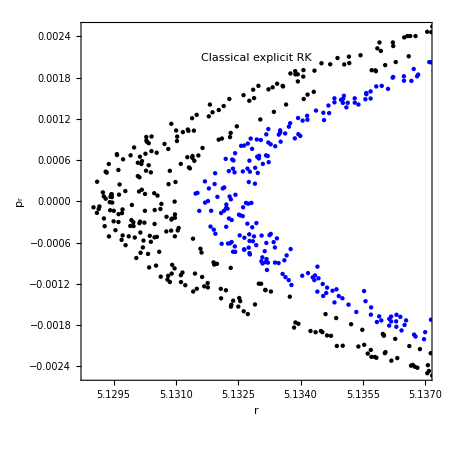

```mathematica
q=-1.7; J=0.4; Ttime=500000; R1=5.131; R2=5.133; nn=R2-R1; LL=0.999; EE=0.95;

crkamat={{1/2},{0,1/2},{0,0,1}};
crkbvec={1/6,1/3,1/3,1/6};
crkcvec={1/2,1/2,1};
ClassicalRungeKuttaCoefficients[4,p_]:=N[{crkamat,crkbvec,crkcvec},p];

myMethod={"ExplicitRungeKutta","DifferenceOrder"->4,"Coefficients"->ClassicalRungeKuttaCoefficients};

DATA1=Table[GiveMeTra[RR,θ0,EE,LL,Ttime],{RR,R1,R2,nn}];
pic1a=ListPlot[DATA1,PlotStyle->{{Black,PointSize[ptSZ]},{Blue,PointSize[ptSZ]}},Frame->True,Axes->False,BaseStyle->fontyW,ImageSize->450,AspectRatio->1,PlotRange->{{5.12888,5.137},{-0.0025,0.0025}},FrameLabel->{"r","p_r"},Epilog->{{Black,Text["Classical explicit RK",Scaled[{0.5,0.9}]]}}]
```

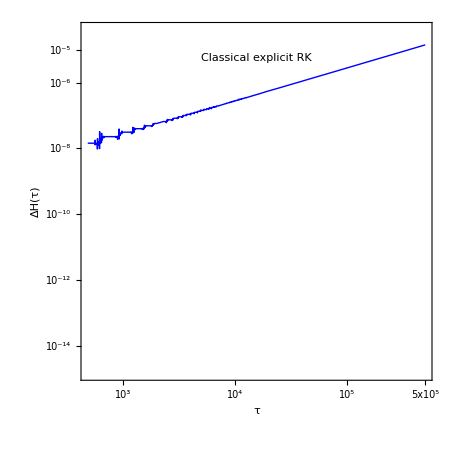

```mathematica
picb1=LogLogPlot[Abs[Hexact-Happrox]/.draha,{τ,0,end},Frame->True,PlotStyle->Blue,FrameLabel->{"τ","ΔH(τ)"},ImageSize->450,BaseStyle->fontyW,AspectRatio->1,Epilog->{{Black,Text["Classical explicit RK",Scaled[{0.5,0.9}]]}},PlotRange->{{0,end},{1.5 10^-15,4.1 10^-5}},FrameTicks->{{{{10^-16,"10^-16"},{10^-14,"10^-14"},{ 10^-12,"10^-12"},{ 10^-10,"10^-10"},{ 10^-8,"10^-8"},{ 10^-6,"10^-6"},{ 10^-5,"10^-5"}},Automatic},{{{10^3,"10^3"},{10^4,"10^4"},{ 10^5,"10^5"},{5 10^5,"5x10^5"}},Automatic}}]
```

## 2 - Classical explicit RK method with projection technique --- non-symplectic

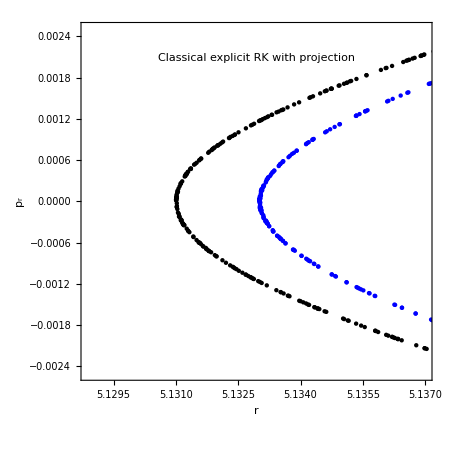

```mathematica
crkamat={{1/2},{0,1/2},{0,0,1}};
crkbvec={1/6,1/3,1/3,1/6};
crkcvec={1/2,1/2,1};
ClassicalRungeKuttaCoefficients[4,p_]:=N[{crkamat,crkbvec,crkcvec},p];

myMethod={"Projection", Method->{"ExplicitRungeKutta","DifferenceOrder"->4,"Coefficients"->ClassicalRungeKuttaCoefficients},"Invariants"->Happrox};

DATA2=Table[GiveMeTra[RR,θ0,EE,LL,Ttime],{RR,R1,R2,nn}];
pic1b=ListPlot[DATA2,PlotStyle->{{Black,PointSize[ptSZ]},{Blue,PointSize[ptSZ]}},Frame->True,Axes->False,BaseStyle->fontyW,ImageSize->450,AspectRatio->1,PlotRange->{{5.12888,5.137},{-0.0025,0.0025}},FrameLabel->{"r","p_r"},Epilog->{{Black,Text["Classical explicit RK with projection",Scaled[{0.5,0.9}]]}}]
```

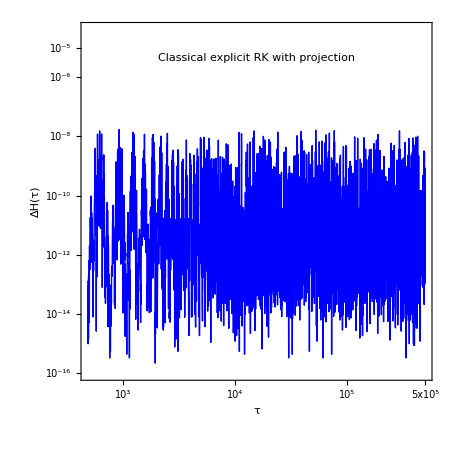

```mathematica
picb2=LogLogPlot[Abs[Hexact-Happrox]/.draha,{τ,0,end},Frame->True,PlotStyle->Blue,FrameLabel->{"τ","ΔH(τ)"},ImageSize->450,BaseStyle->fontyW,AspectRatio->1,Epilog->{{Black,Text["Classical explicit RK with projection",Scaled[{0.5,0.9}]]}},PlotRange->{{0,end},{ 10^-16,4.1 10^-5}},FrameTicks->{{{{10^-16,"10^-16"},{10^-14,"10^-14"},{ 10^-12,"10^-12"},{ 10^-10,"10^-10"},{ 10^-8,"10^-8"},{ 10^-6,"10^-6"},{ 10^-5,"10^-5"}},Automatic},{{{10^3,"10^3"},{10^4,"10^4"},{ 10^5,"10^5"},{5 10^5,"5x10^5"}},Automatic}}]
```

## 3 - Implicit RK method --- symplectic

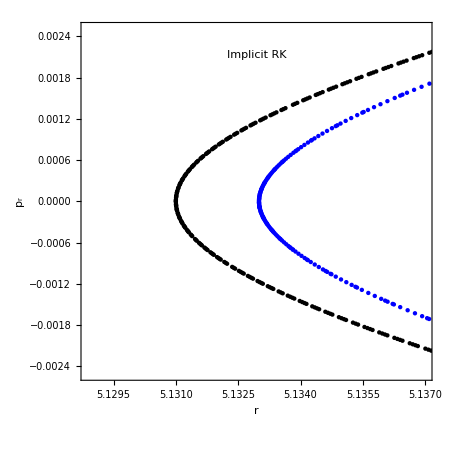

```mathematica
myMethod={"FixedStep",Method->{"ImplicitRungeKutta","DifferenceOrder"->4,"ImplicitSolver"->{"Newton",AccuracyGoal->15,PrecisionGoal->50,"IterationSafetyFactor"->1}}};
DATA3=Table[GiveMeTra[RR,θ0,EE,LL,Ttime],{RR,R1,R2,nn}];

pic1c=ListPlot[DATA3,PlotStyle->{{Black,PointSize[ptSZ]},{Blue,PointSize[ptSZ]}},Frame->True,Axes->False,BaseStyle->fontyW,ImageSize->450,AspectRatio->1,PlotRange->{{5.12888,5.137},{-0.0025,0.0025}},FrameLabel->{"r","p_r"},Epilog->{{Black,Text["Implicit RK",Scaled[{0.5,0.91}]]}}]
```

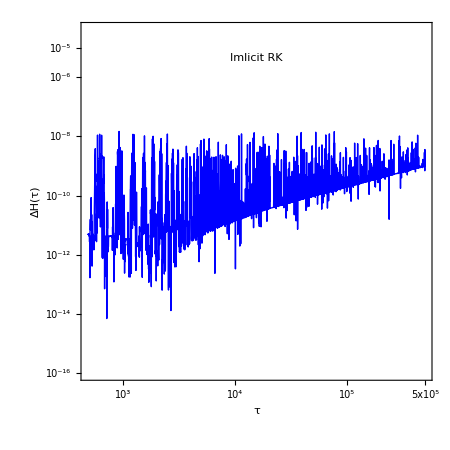

```mathematica
picb3=LogLogPlot[Abs[Hexact-Happrox]/.draha,{τ,0,end},Frame->True,PlotStyle->Blue,FrameLabel->{"τ","ΔH(τ)"},ImageSize->450,BaseStyle->fontyW,AspectRatio->1,Epilog->{{Black,Text["Imlicit RK",Scaled[{0.5,0.9}]]}},PlotRange->{{0,end},{ 10^-16,4.1 10^-5}},FrameTicks->{{{{10^-16,"10^-16"},{10^-14,"10^-14"},{ 10^-12,"10^-12"},{ 10^-10,"10^-10"},{ 10^-8,"10^-8"},{ 10^-6,"10^-6"},{ 10^-5,"10^-5"}},Automatic},{{{10^3,"10^3"},{10^4,"10^4"},{ 10^5,"10^5"},{5 10^5,"5x10^5"}},Automatic}}]
```

## all Figs

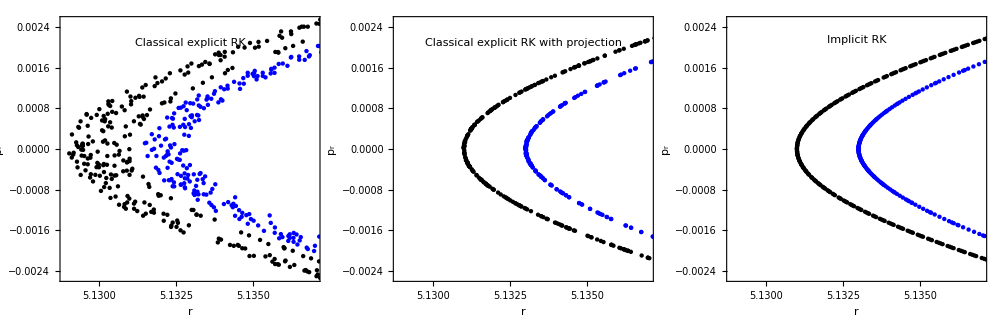

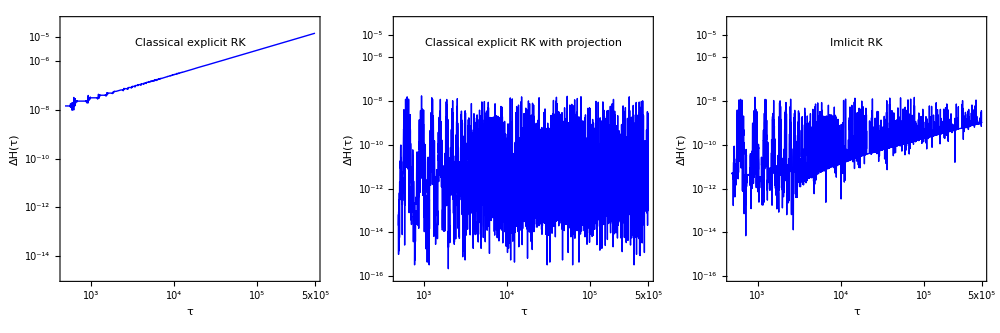

```mathematica
picA=GraphicsRow[{pic1a,pic1b,pic1c},ImageSize->1000,Spacings->0]
picB=GraphicsRow[{picb1,picb2,picb3},ImageSize->1000,Spacings->0]
```

## Some Builtin methods of order 4

## 1- Explicit RK method --- non-symplectic

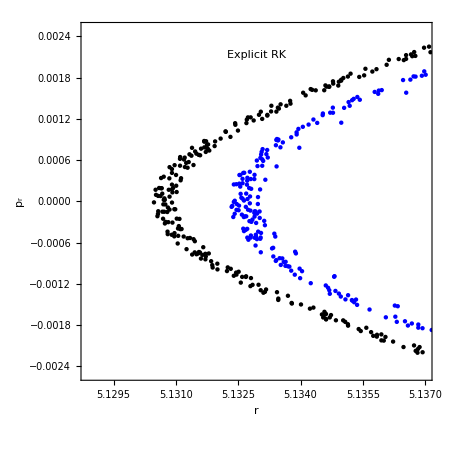

```mathematica
myMethod={"ExplicitRungeKutta","DifferenceOrder"->4};
DATA4=Table[GiveMeTra[RR,θ0,EE,LL,Ttime],{RR,R1,R2,nn}];

pic1d=ListPlot[DATA4,PlotStyle->{{Black,PointSize[ptSZ]},{Blue,PointSize[ptSZ]}},Frame->True,Axes->False,BaseStyle->fontyW,ImageSize->450,AspectRatio->1,PlotRange->{{5.12888,5.137},{-0.0025,0.0025}},FrameLabel->{"r","p_r"},Epilog->{{Black,Text["Explicit RK",Scaled[{0.5,0.91}]]}}]
```

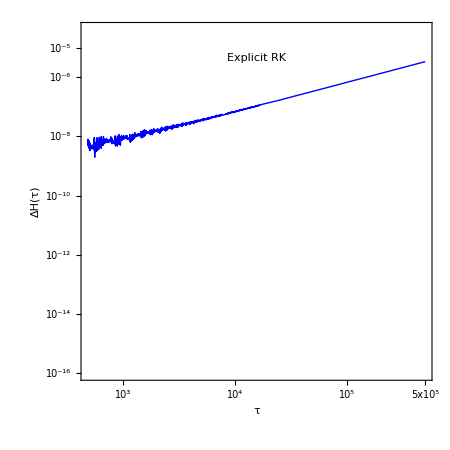

```mathematica
picb4=LogLogPlot[Abs[Hexact-Happrox]/.draha,{τ,0,end},Frame->True,PlotStyle->Blue,FrameLabel->{"τ","ΔH(τ)"},ImageSize->450,BaseStyle->fontyW,AspectRatio->1,Epilog->{{Black,Text["Explicit RK",Scaled[{0.5,0.9}]]}},PlotRange->{{0,end},{ 10^-16,4.1 10^-5}},FrameTicks->{{{{10^-16,"10^-16"},{10^-14,"10^-14"},{ 10^-12,"10^-12"},{ 10^-10,"10^-10"},{ 10^-8,"10^-8"},{ 10^-6,"10^-6"},{ 10^-5,"10^-5"}},Automatic},{{{10^3,"10^3"},{10^4,"10^4"},{ 10^5,"10^5"},{5 10^5,"5x10^5"}},Automatic}}]
```

## 2 - Explicit RK method with projection and StiffnessSwitching --- non-symplectic

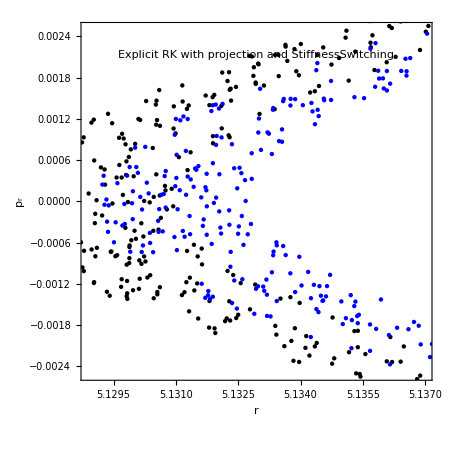

```mathematica
myMethod={"StiffnessSwitching", Method->{ {"Projection", Method->{"ExplicitRungeKutta","DifferenceOrder"->4},"Invariants"->Happrox},Automatic}};

DATA5=Table[GiveMeTra[RR,θ0,EE,LL,Ttime],{RR,R1,R2,nn}];

pic1e=ListPlot[DATA5,PlotStyle->{{Black,PointSize[ptSZ]},{Blue,PointSize[ptSZ]}},Frame->True,Axes->False,BaseStyle->fontyW,ImageSize->450,AspectRatio->1,PlotRange->{{5.12888,5.137},{-0.0025,0.0025}},FrameLabel->{"r","p_r"},Epilog->{{Black,Text["Explicit RK with projection and StiffnessSwitching",Scaled[{0.5,0.91}]]}}]
```

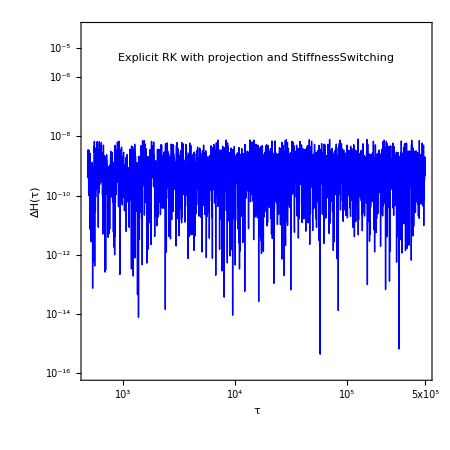

```mathematica
picb5=LogLogPlot[Abs[Hexact-Happrox]/.draha,{τ,0,end},Frame->True,PlotStyle->Blue,FrameLabel->{"τ","ΔH(τ)"},ImageSize->450,BaseStyle->fontyW,AspectRatio->1,Epilog->{{Black,Text["Explicit RK with projection and StiffnessSwitching",Scaled[{0.5,0.9}]]}},PlotRange->{{0,end},{ 10^-16,4.1 10^-5}},FrameTicks->{{{{10^-16,"10^-16"},{10^-14,"10^-14"},{ 10^-12,"10^-12"},{ 10^-10,"10^-10"},{ 10^-8,"10^-8"},{ 10^-6,"10^-6"},{ 10^-5,"10^-5"}},Automatic},{{{10^3,"10^3"},{10^4,"10^4"},{ 10^5,"10^5"},{5 10^5,"5x10^5"}},Automatic}}]
```

## 3 - Explicit RK method with FixedStep method

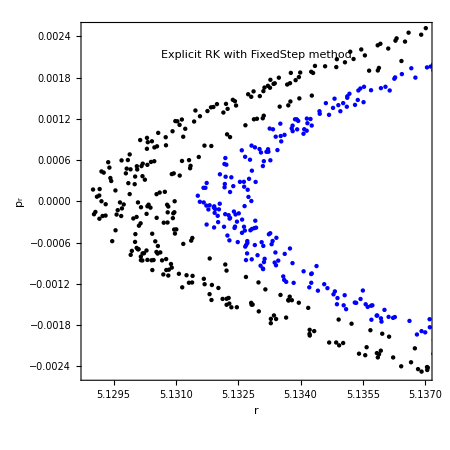

```mathematica
myMethod={"FixedStep",Method->{"ExplicitRungeKutta","DifferenceOrder"->4}};

DATA6=Table[GiveMeTra[RR,θ0,EE,LL,Ttime],{RR,R1,R2,nn}];

pic1f=ListPlot[DATA6,PlotStyle->{{Black,PointSize[ptSZ]},{Blue,PointSize[ptSZ]}},Frame->True,Axes->False,BaseStyle->fontyW,ImageSize->450,AspectRatio->1,PlotRange->{{5.12888,5.137},{-0.0025,0.0025}},FrameLabel->{"r","p_r"},Epilog->{{Black,Text["Explicit RK with FixedStep method",Scaled[{0.5,0.91}]]}}]
```

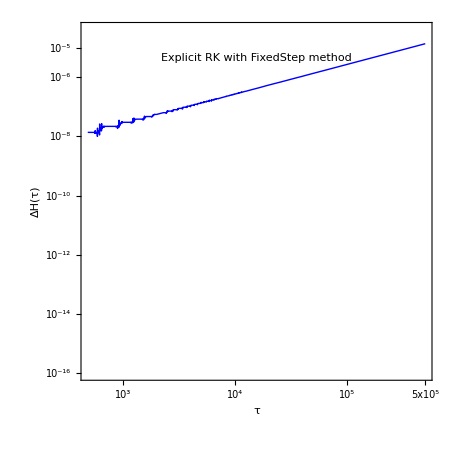

```mathematica
picb6=LogLogPlot[Abs[Hexact-Happrox]/.draha,{τ,0,end},Frame->True,PlotStyle->Blue,FrameLabel->{"τ","ΔH(τ)"},ImageSize->450,BaseStyle->fontyW,AspectRatio->1,Epilog->{{Black,Text["Explicit RK with FixedStep method",Scaled[{0.5,0.9}]]}},PlotRange->{{0,end},{ 10^-16,4.1 10^-5}},FrameTicks->{{{{10^-16,"10^-16"},{10^-14,"10^-14"},{ 10^-12,"10^-12"},{ 10^-10,"10^-10"},{ 10^-8,"10^-8"},{ 10^-6,"10^-6"},{ 10^-5,"10^-5"}},Automatic},{{{10^3,"10^3"},{10^4,"10^4"},{ 10^5,"10^5"},{5 10^5,"5x10^5"}},Automatic}}]
```

## all Figs.

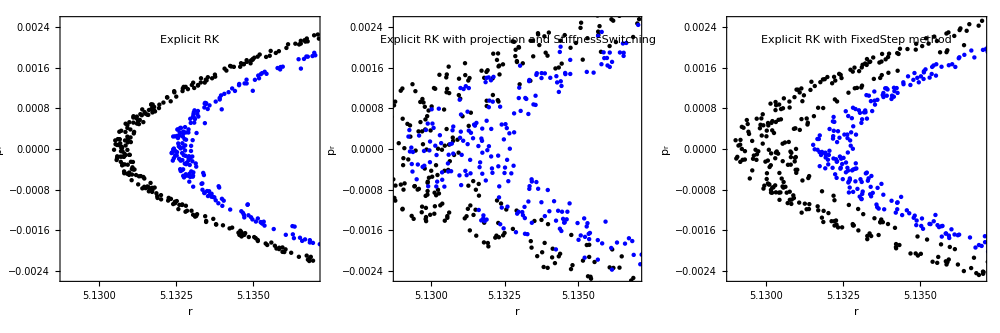

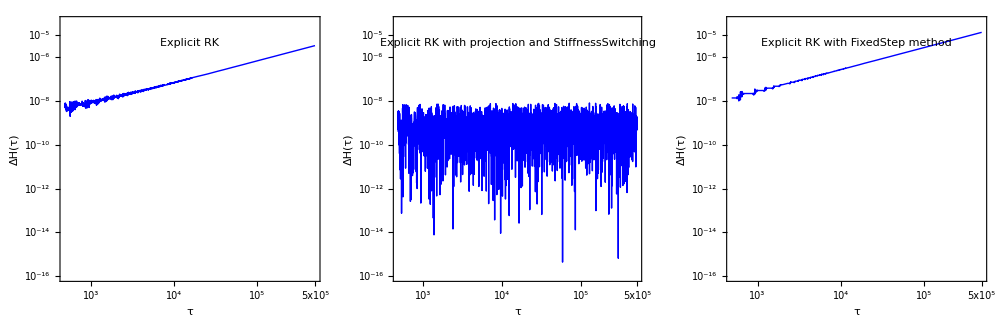

```mathematica
picC=GraphicsRow[{pic1d,pic1e,pic1f},ImageSize->1000,Spacings->0]
picD=GraphicsRow[{picb4,picb5,picb6},ImageSize->1000,Spacings->0]
```

```mathematica
{picA,picC,picB,picD}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}